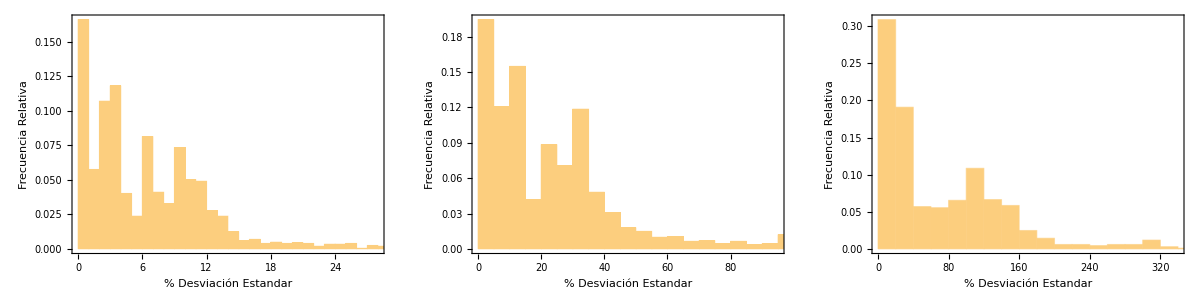

```mathematica
y = "/home/fabianact/ActualTesis/Tesis/ModelosPresentados/SinCompetencia";
SetDirectory["/home/fabianact/ActualTesis/Tesis/ModelosPresentados/Distribución"];
SetOptions[ListPlot,BaseStyle->{FontSize->20}];
pub1= Import[y<>"/averageResults/data-por-0.01-turtles.csv"];
histo1=Show[Histogram[Flatten[pub1],Automatic,"Probability",ImageSize->300], Frame->{{True, False},{True, False}},FrameTicks->{{All,None},{All,None}}, FrameLabel->{"% Desviación Estandar","Frecuencia Relativa"}];
pub2= Import[y<>"/averageResults/data-por-0.001-turtles.csv"];
histo2=Show[Histogram[Flatten[pub2], Automatic,"Probability",ImageSize->300], Frame->{{True, False},{True, False}},FrameTicks->{{All,None},{All,None}}, FrameLabel->{"% Desviación Estandar","Frecuencia Relativa"}];
pub3= Import[y<>"/averageResults/data-por-0.0001-turtles.csv"];
histo3=Show[Histogram[Flatten[pub3],Automatic,"Probability",ImageSize->300], Frame->{{True, False},{True, False}},FrameTicks->{{All,None},{All,None}}, FrameLabel->{"% Desviación Estandar","Frecuencia Relativa"}];
grilla=Grid[{{histo1,histo2,histo3}}]
Export["DesvestaGridSinCompetencia.png",grilla];
```

```mathematica
.14
```

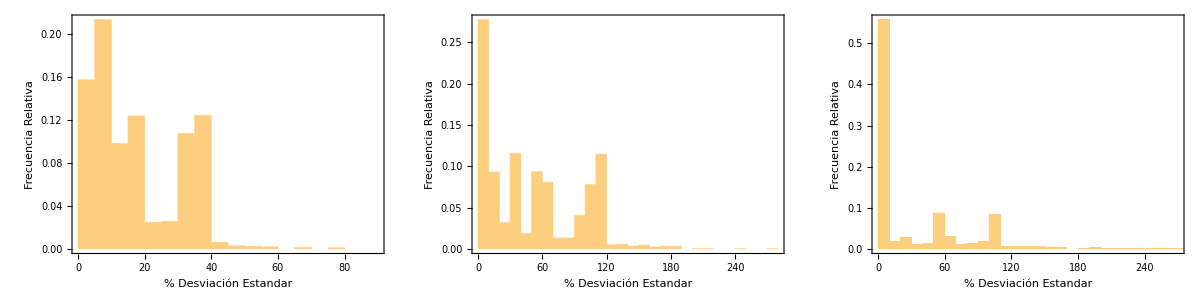

```mathematica
y = "/home/fabianact/ActualTesis/Tesis/ModelosPresentados/ConCompetencia";
SetDirectory["/home/fabianact/ActualTesis/Tesis/ModelosPresentados/Distribución"];
SetOptions[ListPlot,BaseStyle->{FontSize->20}];
pub1= Import[y<>"/averageResults/data-por-0.01-turtles.csv"];
histo1=Show[Histogram[Flatten[pub1],Automatic,"Probability",ImageSize->300], Frame->{{True, False},{True, False}},FrameTicks->{{All,None},{All,None}}, FrameLabel->{"% Desviación Estandar","Frecuencia Relativa"}];
pub2= Import[y<>"/averageResults/data-por-0.001-turtles.csv"];
histo2=Show[Histogram[Flatten[pub2], Automatic,"Probability",ImageSize->300], Frame->{{True, False},{True, False}},FrameTicks->{{All,None},{All,None}}, FrameLabel->{"% Desviación Estandar","Frecuencia Relativa"}];
pub3= Import[y<>"/averageResults/data-por-0.0001-turtles.csv"];
histo3=Show[Histogram[Flatten[pub3], Automatic,"Probability",ImageSize->300], Frame->{{True, False},{True, False}},FrameTicks->{{All,None},{All,None}}, FrameLabel->{"% Desviación Estandar","Frecuencia Relativa"}];
grilla=Grid[{{histo1,histo2,histo3}}]
Export["DesvestaGridconCompetencia.png",grilla];
```